AirBot

```mathematica
Quit[];
```

```mathematica
(*simulation parameters*)
tEnd=20;

(*physical parameters*)
mb=0.300;(*kg*)
rb=0.050;(*m*)
Ib=0.5*mb*rb^2
mw=0.04;
rw=0.03;
Iw=0.5*mw*rw^2
μ=0.1+RandomReal[{0,0.3}];
mTotal=mb+mw
g=9.8;
```

0.000375

0.000018

0.34

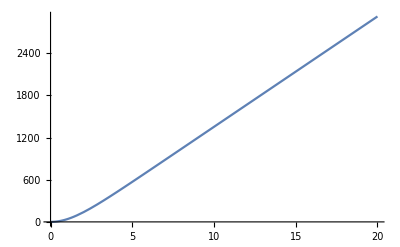

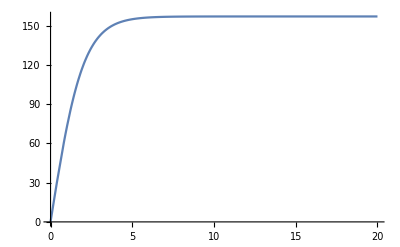

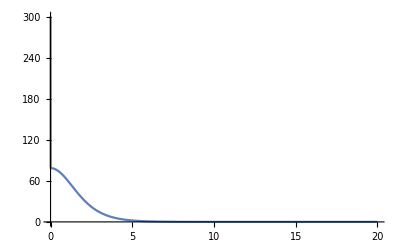

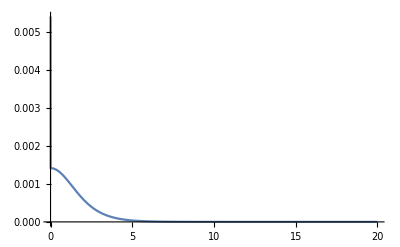

```mathematica
(*reaction wheel motion*)
wheelODE=θw'[t]==50*2*Pi*(1/(1+E^-t)-0.5);(*50 RPS*)
wheelInitCon=θw[0]==0;
wheelSol=NDSolve[{wheelODE,wheelInitCon},{θw[t],θw'[t],θw''[t]},{t,0,tEnd}][[1]];
τw=Iw*θw''[t]/.wheelSol;
Plot[θw[t]/.wheelSol,{t,0,tEnd},PlotRange->Full,PlotLegends->θw[t]]
Plot[θw'[t]/.wheelSol,{t,0,tEnd},PlotRange->Full,PlotLegends->θw'[t]]
Plot[θw''[t]/.wheelSol,{t,0,tEnd},PlotRange->Full,PlotLegends->θw''[t]]
Plot[τw,{t,0,tEnd},PlotRange->Full,PlotLegends->"τw"]
```

```mathematica
μ*(2/3)*rb*mTotal*g
```

0.0152695

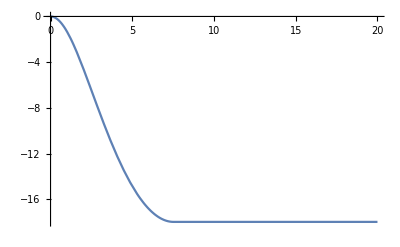

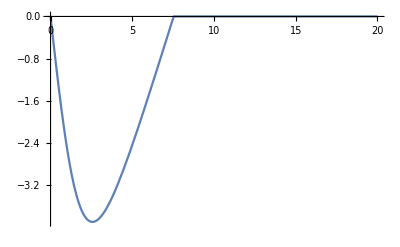

```mathematica
(*baseODE=θb''[t]==(-Sign[θb'[t]]*μ*(2/3)*rb*mTotal*g-τw)/Ib;*)
baseODE=θb''[t]==(-Sign[θb'[t]]*1*Ib-τw)/Ib(*-θb'[t]*RandomReal[{0,0.01}]/Ib*);
initcon1=θb[0]==0;
initcon2=θb'[0]==0;
sol=NDSolve[{baseODE,initcon1,initcon2},{θb[t],θb'[t]},{t,0,tEnd}][[1]];
Plot[θb[t]/.sol,{t,0,tEnd},PlotRange->Full,PlotLegends->θb[t]]
Plot[θb'[t]/.sol,{t,0,tEnd},PlotRange->Full,PlotLegends->θb'[t]]
```

```mathematica
list={Graphics3D[Cuboid[]],Graphics[Rectangle[]],Graphics[Line[{{0,0},{1,1}}]],Graphics[Point[{0,0}]]};
ListAnimate[list,AnimationRunning->False]
```

```mathematica
list=Table[Graphics3D[Rotate[{Cylinder[{{0,0,0},{0,0,0.02}},0.05],Line[{{0,0,0.02},{0.05,0,0.02}}]},i Degree,{0,0,1}]],{i,0,360,1}];
ListAnimate[list,AnimationRunning->False]
```